# Tutorial dasar Mathematica

## Penulisan operasi matematika

```mathematica
10^3
```

1000

```mathematica
Power[10,3]
```

1000

```mathematica
10^3
```

1000

```mathematica
a={{1,3},{4,2}}
```

{{1,3},{4,2}}

```mathematica
a
```

{{1,3},{4,2}}

```mathematica
%//MatrixForm (* hasil sebelumnya dipanggil dengan % kemudian dijadikan input fungsi MatrixForm *)
```

(1 | 3
4 | 2)

```mathematica
b={{1,4},{6,6}}
```

{{1,4},{6,6}}

```mathematica
MatrixForm[a.b]
```

(19 | 22
16 | 28)

```mathematica
Table[Subscript[x,(10i+j)],{i,3},{j,3}] (* Table melakukan looping i 1-3 dengan didalam looping i terdapat looping j 
1-3 (Nested Loop) *)
```

{{x_11,x_12,x_13},{x_21,x_22,x_23},{x_31,x_32,x_33}}

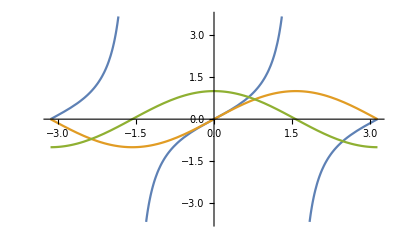

```mathematica
Plot[{Tan[x],Sin[x],Cos[x]},{x,-Pi,Pi}]
```

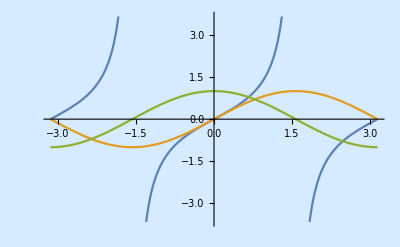

```mathematica
Show[%13,Background->RGBColor[0.84,0.92,1.]]
```

```mathematica
x/.Solve[x^2+4==0,x][[1]] (* Menyelesaikan persamaan tertentu (hasil dalam bentuk array, kemudian diambil suku pertama ([[1]]) dan diambil nilai x nya (x/.) *)
```

-2 ⅈ

```mathematica
(#[[3]]+#[[2]])&[Range[3]] (* ganti # dengan Range[3] *)
```

5

```mathematica
Range[5]
```

{1,2,3,4,5}

```mathematica
Graphics3D[#]&[{Cone[],Cuboid[]}]
```

-Graphics3D-

```mathematica
a=Map[Graphics3D[#]&,{Cone[],Cuboid[]}]
```

{-Graphics3D-,-Graphics3D-}

```mathematica
a[[1]]
```

-Graphics3D-

```mathematica
f=Function[{x,y}, x^2+y^2] (* Membuat fungsi dengan bentuk x^2+y^2 *)
```

Function[{x,y},x^2+y^2]

```mathematica
f[3,2]
```

13

```mathematica
fungsi = (3+#)&
```

3+#1&

```mathematica
fungsi[10]
```

13